```mathematica
<<X`;(*import package X to calcualate Feynman Functions*)
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

## Calculate the loop contribution of the new charged vector couple only to muon in muon decay

```mathematica
Spur[((A+B)𝟙+(A-B)γ5),Subscript[γ, ν],(p.γ+m*𝟙),ℙR,Subscript[γ, μ],γ.(p-q)]
```

8 A p_μ p_ν-4 A p_ν q_μ-4 A p_μ q_ν-4 A p.p 𝕘_(μ,ν)+4 A p.q 𝕘_(μ,ν)+4 ⅈ A ε_(μ,ν,{p},{q})

```mathematica
LoopIntegrate[Subscript[p, μ] Subscript[q, ν],p,{p,m},{(p-q),0}]-2*LoopIntegrate[Subscript[p, μ] Subscript[p, ν],p,{p,m},{(p-q),0}]+Subscript[𝕘, μ,ν](LoopIntegrate[p.p,p,{p,m},{(p-q),0}]-LoopIntegrate[p.q,p,{p,m},{(p-q),0}])
```

𝕘_(μ,ν) (1/2 PVA[0,0]+1/2 PVA[0,m]+m^2 PVB[0,0,q.q,m,0]-(m^2/2+(q.q)/2) PVB[0,0,q.q,m,0])-q_μ q_ν PVB[0,1,q.q,m,0]-2 (q_μ q_ν PVB[0,2,q.q,m,0]+𝕘_(μ,ν) PVB[1,0,q.q,m,0])

```mathematica
( PVA[0,m]+m^2 PVB[0,0,q.q,m,0]+q.q*PVB[0,0,q.q,m,0]-4PVB[1,0,q.q,m,0])//LoopRefine (*Check whether wrong sign in term q.q*PVB[0,0,q.q,m,0]?*)
```

(3 m^4+6 m^2 q.q+26 (q.q)^2)/(9 q.q)+1/3 (3 m^2+4 q.q) (1/ϵ+Log[µ^2/m^2])+((-m^6-3 m^2 (q.q)^2+4 (q.q)^3) Log[m^2/(m^2-q.q)])/(3 (q.q)^2)

```mathematica
Plfunc[x_,m_]:=((-m^6-3 m^2 (x)^2+4 (x)^3) Log[m^2/(m^2-x)])/(3 (x)^2)+(3 m^4+6 m^2 x+26 (x)^2)/(9 x);
Limit[Plfunc[x,0.1],x->0.1^2]
```

0.0388889

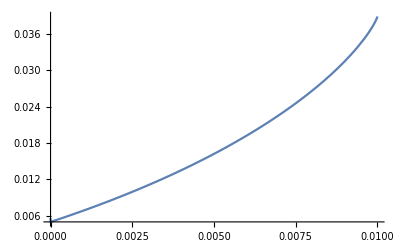

```mathematica
Plot[Plfunc[x,0.1],{x,0,0.1^2}]
```

## Calculate the decay rate

```mathematica
Spur[((SuperStar[A]+SuperStar[B])𝟙+(SuperStar[A]-SuperStar[B])γ5),Subscript[γ, μ],(k.γ+m*𝟙),((A+B)𝟙+(A-B)γ5),Subscript[γ, μ],γ.(q-k)]+Spur[((SuperStar[A]+SuperStar[B])𝟙+(SuperStar[A]-SuperStar[B])γ5),γ.q,(k.γ+m*𝟙),((A+B)𝟙+(A-B)γ5),γ.q,γ.(q-k)]/mV^2//.{q.q->mV^2,k.k->m^2,𝒹 ->4}//Simplify
```

(8 (3 m^2 mV^2-mV^2 k.q-2 (k.q)^2) (A A^*+B B^*))/mV^2

```mathematica
%//.k.q->(mV^2+m^2)/2//Simplify
```

-(4 (m^4+m^2 mV^2-2 mV^4) (A A^*+B B^*))/mV^2

```mathematica
Spur[((SuperStar[A]+SuperStar[B])𝟙+(SuperStar[B]-SuperStar[A])γ5),(k.γ+m*𝟙),((A+B)𝟙+(A-B)γ5),γ.(q-k)]//.{q.q->mV^2,k.k->m^2,𝒹 ->4,k.q->(mV^2+m^2)/2}//Simplify
```

-4 (m^2-mV^2) (A A^*+B B^*)

## Finding eigenvalue and eigenvector of Schwinger model

```mathematica
Subscript[σ, x] = PauliMatrix[1];
Subscript[σ, y] = PauliMatrix[2];
Subscript[σ, z] = PauliMatrix[3];
i= IdentityMatrix[2];
SubPlus[σ]=(Subscript[σ, x]+I*Subscript[σ, y])/2;
SubMinus[σ]=(Subscript[σ, x]-I*Subscript[σ, y])/2;
H[mu_,x_]:=mu*(-KroneckerProduct[Subscript[σ, z],i,i]+KroneckerProduct[i,Subscript[σ, z],i]-3KroneckerProduct[i,i,Subscript[σ, z]])-KroneckerProduct[Subscript[σ, z],i,i]+x*(KroneckerProduct[SubPlus[σ],SubMinus[σ],i]+KroneckerProduct[SubMinus[σ],SubPlus[σ],i]+KroneckerProduct[i,SubPlus[σ],SubMinus[σ]]+KroneckerProduct[i,SubMinus[σ],SubPlus[σ]])+KroneckerProduct[Subscript[σ, z],Subscript[σ, z],i];(*mu=(2m)/(g^2 a),x =2/(g^2 a^2)*)
p[mu_,x_]:=Transpose[Eigenvectors[H[mu,x]]]
DiaH[mu_,x_]:=Inverse[p[mu,x]].H[mu,x].p[mu,x];
```

```mathematica
N[DiaH[1,1]]//Simplify//MatrixForm
```

(-10.0066 | 0. | 0. | 4.44089×10^-16 | 0. | 0. | 0. | 0.
0. | 8.40312 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 5. | 0. | 0. | 0. | 0. | 0.
-2.10942×10^-15 | 0. | 0. | 4.77647 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -4.40312 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -3. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1. | 0.
3.66374×10^-15 | 0. | 0. | -6.93889×10^-16 | 0. | 0. | 0. | 0.230143)

## The loop contribution of the Triplet Higgs in pion decay

```mathematica
(*k1->neutrino momentum, k2-> lepton momentum, mf-> mass of lepton, md-> mass of triplet Higgs*)
```

```mathematica
(*Subscript[M, 1]^+,Subscript[Γ^μ, W]*)
(LoopIntegrate[DiracMatrix[γ.(k1-q)+ml 𝟙,Subscript[γ, μ],ℙL,γ.(k2+q)],q,{q,md},{k1-q,ml},{k2+q,0},DiracAlgebra->True])/.k1.k1->0/.k2.k2->mL^2
```

DiracMatrix[γ_μ,γ.k2,ℙR] (ml PVC[0,0,0,0,mL^2+2 k1.k2,mL^2,md,ml,0]+ml PVC[0,0,1,0,mL^2+2 k1.k2,mL^2,md,ml,0])+DiracMatrix[γ.k2,ℙR] k2_μ (-2 PVC[0,0,1,0,mL^2+2 k1.k2,mL^2,md,ml,0]-2 PVC[0,0,2,0,mL^2+2 k1.k2,mL^2,md,ml,0])+DiracMatrix[γ_μ,γ.k1,γ.k2,ℙR] (-PVC[0,0,0,0,mL^2+2 k1.k2,mL^2,md,ml,0]-PVC[0,0,1,0,mL^2+2 k1.k2,mL^2,md,ml,0]-PVC[0,1,0,0,mL^2+2 k1.k2,mL^2,md,ml,0])-ml DiracMatrix[γ_μ,γ.k1,ℙR] PVC[0,1,0,0,mL^2+2 k1.k2,mL^2,md,ml,0]+2 DiracMatrix[γ.k1,ℙR] k2_μ PVC[0,1,1,0,mL^2+2 k1.k2,mL^2,md,ml,0]+DiracMatrix[γ.k2,ℙR] k1_μ (2 (PVC[0,0,0,0,mL^2+2 k1.k2,mL^2,md,ml,0]+PVC[0,0,1,0,mL^2+2 k1.k2,mL^2,md,ml,0]+PVC[0,1,0,0,mL^2+2 k1.k2,mL^2,md,ml,0])+2 PVC[0,1,1,0,mL^2+2 k1.k2,mL^2,md,ml,0])+DiracMatrix[γ.k1,ℙR] k1_μ (-2 PVC[0,1,0,0,mL^2+2 k1.k2,mL^2,md,ml,0]-2 PVC[0,2,0,0,mL^2+2 k1.k2,mL^2,md,ml,0])+DiracMatrix[γ_μ,ℙR] (PVB[0,0,mL^2+2 k1.k2,ml,0]+md^2 PVC[0,0,0,0,mL^2+2 k1.k2,mL^2,md,ml,0]+mL^2 PVC[0,0,1,0,mL^2+2 k1.k2,mL^2,md,ml,0]-2 PVC[1,0,0,0,mL^2+2 k1.k2,mL^2,md,ml,0])

```mathematica
LoopRefine[%,Part->UVDivergent]
```

DiracMatrix[γ_μ,ℙR]/(2 ϵ)

```mathematica
(*Subscript[M, 3]^+, Subscript[G, l]^+*)
LoopIntegrate[DiracMatrix[γ.(k1-q)+ml 𝟙],q,{q,md},{k1-q,ml},DiracAlgebra->True]/.k1.k1->0/.k2.k2->mL^2
```

ml DiracMatrix[] PVB[0,0,0,md,ml]+DiracMatrix[γ.k1] (PVB[0,0,0,md,ml]+PVB[0,1,0,md,ml])

```mathematica
LoopRefine[%,Part->UVDivergent]
```

(ml DiracMatrix[])/ϵ+DiracMatrix[γ.k1]/(2 ϵ)

```mathematica
(*Subscript[M, 2]^(++),Subscript[G, l]^(++)*)
LoopIntegrate[DiracMatrix[γ.(k2+q)+ml 𝟙],q,{q,md},{k2+q,ml},DiracAlgebra->True]/.k1.k1->0/.k2.k2->mL^2
```

ml DiracMatrix[] PVB[0,0,mL^2,md,ml]+DiracMatrix[γ.k2] (PVB[0,0,mL^2,md,ml]+PVB[0,1,mL^2,md,ml])

```mathematica
LoopRefine[%,Part->UVDivergent]
```

(ml DiracMatrix[])/ϵ+DiracMatrix[γ.k2]/(2 ϵ)

```mathematica
(*Subscript[M, 3]^0,Subscript[G, v]^0*)
LoopIntegrate[DiracMatrix[γ.(k1-q)],q,{q,md},{k1-q,0},DiracAlgebra->True]/.k1.k1->0/.k2.k2->mL^2
```

DiracMatrix[γ.k1] (PVB[0,0,0,md,0]+PVB[0,1,0,md,0])

```mathematica
LoopRefine[%,Part->UVDivergent]
```

DiracMatrix[γ.k1]/(2 ϵ)

```mathematica
(*Subscript[M, 2]^+,Subscript[G, v]^+*)
LoopIntegrate[DiracMatrix[γ.(k2+q)],q,{q,md},{k2+q,0},DiracAlgebra->True]/.k1.k1->0/.k2.k2->mL^2
```

DiracMatrix[γ.k2] (PVB[0,0,mL^2,md,0]+PVB[0,1,mL^2,md,0])

```mathematica
LoopRefine[%,Part->UVDivergent]
```

DiracMatrix[γ.k2]/(2 ϵ)

```mathematica
(*Subscript[M, 4,5],Subscript[Γ, WΔ]*)
LoopIntegrate[(k1+k2).(2q+k1-k2)DiracMatrix[γ.q],q,{q,ml},{k2-q,md},{k1+q,md},DiracAlgebra->True]/.k1.k1->0/.k2.k2->mL^2
```

-DiracMatrix[γ.k1] PVB[0,1,0,ml,md]-DiracMatrix[γ.k2] PVB[0,1,mL^2,ml,md]

```mathematica
LoopRefine[%,Part->UVDivergent]
```

DiracMatrix[γ.k1]/(2 ϵ)+DiracMatrix[γ.k2]/(2 ϵ)

```mathematica
(*ϵ^(1-loop) function evaluated*)
f[md_,mpi_]:=LoopRefine[md^2*PVC[0,0,0,0,mpi^2,0,md,0,0]+mpi^2*(2PVC[0,0,0,0,mpi^2,0,md,0,0]+2PVC[0,1,0,0,mpi^2,0,md,0,0]+PVC[0,0,1,0,mpi^2,0,md,0,0]+PVC[0,1,1,0,mpi^2,0,md,0,0]-PVC[0,0,2,0,mpi^2,0,md,0,0])+PVB[0,0,mpi^2,0,0]-2PVC[1,0,0,0,mpi^2,0,md,0,0]-PVB[0,0,0,md,0]-PVB[0,1,0,md,0]]
fH2[mh0_,mh_]:=LoopRefine[PVB[0,0,0,mh0,0]+PVB[0,1,0,mh0,0]-PVB[0,0,0,mh,0]-PVB[0,1,0,mh,0]]
```

```mathematica
f[md,mpi]//Simplify
fH2[mh0,mh]//Simplify
```

4+1/3 (1+(2 md^2)/mpi^2) π^2+4 Log[-md^2/mpi^2]+(1+(2 md^2)/mpi^2) Log[-md^2/mpi^2]^2+(2+(4 md^2)/mpi^2) PolyLog[2,1+md^2/mpi^2]

1/2 Log[mh^2/mh0^2]

```mathematica
g[md_,mpi_]:=4+1/3 (1+(2 md^2)/mpi^2) π^2+4 Log[-md^2/mpi^2]+(1+(2 md^2)/mpi^2) Log[-md^2/mpi^2]^2+(2+(4 md^2)/mpi^2) PolyLog[2,1+md^2/mpi^2]
gH2[mh0_,mh_]:=1/2 Log[mh^2/mh0^2]
```

```mathematica
N[Re[g[100,1/10]]]
N[Re[gH2[1000,100]]]
```

-9.574×10^-7

-2.30259

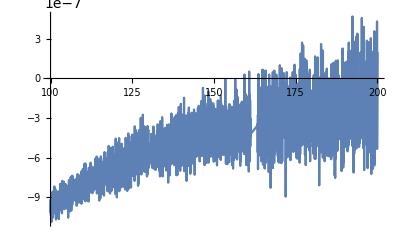

```mathematica
Plot[Re[g[x,0.1]],{x,100,200}]
```

```mathematica
N[(2+(4*100^2)/1^2) PolyLog[2,1+100^2/1^2]]
```

-1.56513×10^6-1.15748×10^6 ⅈ

```mathematica
Series[4+1/3 (1+2 x^2) π^2+4 Log[-x^2]+(1+2 x^2) Log[-x^2]^2+(2+4 x^2) PolyLog[2,1+x^2],{x,0,2}]
```

((4+(2 π^2)/3+4 Log[-x^2]+Log[-x^2]^2)+O[x]^2)+Floor[-Arg[x]/π] (-4 ⅈ π x^2-6 ⅈ π x^4+O[x]^5)

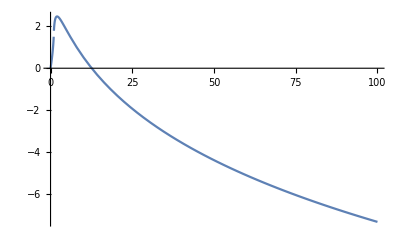

```mathematica
Plot[{Re[PolyLog[2,x]]},{x,0,100}]
```

```mathematica
LoopRefineSeries[PVB[0,1,0,md,ml],{md,Infinity,2},Analytic->True]
```

(-3/4+Log[md]+1/2 (-1/ϵ-Log[µ^2]))+(-(3 ml^2)/2+2 ml^2 Log[md]-ml^2 (1/ϵ+Log[µ^2]))/md^2+O[1/md]^3

```mathematica
LoopRefine[PVB[0,0,0,md,0]]
```

1+1/ϵ+Log[µ^2/md^2]

```mathematica
LoopRefine[PVC[0,0,0,0,mpi^2,0,md,0,0]]
```

π^2/(6 mpi^2)+(Log[-md^2/mpi^2]^2)/(2 mpi^2)+PolyLog[2,(md^2+mpi^2)/mpi^2]/mpi^2

```mathematica
PVC[0,0,0,0,1^2,0,100,0,0]//LoopRefine
```

-π^2/3+ⅈ π Log[10000]+Log[10000]^2/2+PolyLog[2,10001]

## Zee model

### 1) Drafting

```mathematica
ClearAll["Global`*"]
```

```mathematica
Mν[Mee_,Mμμ_,Mττ_,Mμe_,Mτe_,Mτμ_,θμe_,θτe_,θτμ_]:={{Mee,Mμe*Exp[I*θμe],Mτe*Exp[I*θτe]},{Mμe*Exp[-I*θμe],Mμμ,Mτμ*Exp[I*θτμ]},{Mτe*Exp[-I*θτe],Mτμ*Exp[-I*θτμ],Mττ}};
Eigen[Mee_,Mμμ_,Mττ_,Mμe_,Mτe_,Mτμ_,θμe_,θτe_,θτμ_]:=Eigensystem[Mν[Mee,Mμμ,Mττ,Mμe,Mτe,Mτμ,θμe,θτe,θτμ]];
eigenvalues[Mee_,Mμμ_,Mττ_,Mμe_,Mτe_,Mτμ_,θμe_,θτe_,θτμ_]:=Eigen[Mee,Mμμ,Mττ,Mμe,Mτe,Mτμ,θμe,θτe,θτμ][[1]];
eigenvectors[Mee_,Mμμ_,Mττ_,Mμe_,Mτe_,Mτμ_,θμe_,θτe_,θτμ_]:=Eigen[Mee,Mμμ,Mττ,Mμe,Mτe,Mτμ,θμe,θτe,θτμ][[2]];
```

```mathematica
Mν[Mee,Mμμ,Mττ,Mμe,Mτe,Mτμ,θμe,θτe,θτμ]//MatrixForm
```

(Mee | ⅇ^(ⅈ θμe) Mμe | ⅇ^(ⅈ θτe) Mτe
ⅇ^(-ⅈ θμe) Mμe | Mμμ | ⅇ^(ⅈ θτμ) Mτμ
ⅇ^(-ⅈ θτe) Mτe | ⅇ^(-ⅈ θτμ) Mτμ | Mττ)

```mathematica
eigenvalues
```

{ⅇ^(-ⅈ θμe-ⅈ θτe-ⅈ θτμ) Root[ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mμμ Mτe^2-ⅇ^(2 ⅈ θμe+4 ⅈ θτe+2 ⅈ θτμ) Mμe Mτe Mτμ-ⅇ^(4 ⅈ θμe+2 ⅈ θτe+4 ⅈ θτμ) Mμe Mτe Mτμ+ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mee Mτμ^2+ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mμe^2 Mττ-ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mee Mμμ Mττ+(-ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mμe^2+ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mee Mμμ-ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mτe^2-ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mτμ^2+ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mee Mττ+ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mμμ Mττ) #1+(-ⅇ^(ⅈ θμe+ⅈ θτe+ⅈ θτμ) Mee-ⅇ^(ⅈ θμe+ⅈ θτe+ⅈ θτμ) Mμμ-ⅇ^(ⅈ θμe+ⅈ θτe+ⅈ θτμ) Mττ) #1^2+#1^3&,1],ⅇ^(-ⅈ θμe-ⅈ θτe-ⅈ θτμ) Root[ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mμμ Mτe^2-ⅇ^(2 ⅈ θμe+4 ⅈ θτe+2 ⅈ θτμ) Mμe Mτe Mτμ-ⅇ^(4 ⅈ θμe+2 ⅈ θτe+4 ⅈ θτμ) Mμe Mτe Mτμ+ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mee Mτμ^2+ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mμe^2 Mττ-ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mee Mμμ Mττ+(-ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mμe^2+ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mee Mμμ-ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mτe^2-ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mτμ^2+ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mee Mττ+ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mμμ Mττ) #1+(-ⅇ^(ⅈ θμe+ⅈ θτe+ⅈ θτμ) Mee-ⅇ^(ⅈ θμe+ⅈ θτe+ⅈ θτμ) Mμμ-ⅇ^(ⅈ θμe+ⅈ θτe+ⅈ θτμ) Mττ) #1^2+#1^3&,2],ⅇ^(-ⅈ θμe-ⅈ θτe-ⅈ θτμ) Root[ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mμμ Mτe^2-ⅇ^(2 ⅈ θμe+4 ⅈ θτe+2 ⅈ θτμ) Mμe Mτe Mτμ-ⅇ^(4 ⅈ θμe+2 ⅈ θτe+4 ⅈ θτμ) Mμe Mτe Mτμ+ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mee Mτμ^2+ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mμe^2 Mττ-ⅇ^(3 ⅈ θμe+3 ⅈ θτe+3 ⅈ θτμ) Mee Mμμ Mττ+(-ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mμe^2+ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mee Mμμ-ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mτe^2-ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mτμ^2+ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mee Mττ+ⅇ^(2 ⅈ θμe+2 ⅈ θτe+2 ⅈ θτμ) Mμμ Mττ) #1+(-ⅇ^(ⅈ θμe+ⅈ θτe+ⅈ θτμ) Mee-ⅇ^(ⅈ θμe+ⅈ θτe+ⅈ θτμ) Mμμ-ⅇ^(ⅈ θμe+ⅈ θτe+ⅈ θτμ) Mττ) #1^2+#1^3&,3]}

```mathematica
(*Create a function*)
f[x_,y_,z_,a_,b_,c_]:={{x,a,b},{Conjugate[a],y,c},{Conjugate[b],Conjugate[c],z}};Eigen[x_,y_,z_,a_,b_,c_] := Eigensystem[f[x,y,z,a,b,c]];
eigenvalues[x_,y_,z_,a_,b_,c_]:=Eigen[x,y,z,a,b,c][[1]];
eigenvectors[x_,y_,z_,a_,b_,c_]:=Eigen[x,y,z,a,b,c][[2]];
```

```mathematica
(*Create random data set*)
Arr=RandomReal[{-10,10},{7,6}]
```

{{-7.38039,-0.350875,3.71651,-7.35648,3.65978,8.21324},{4.13562,1.15457,9.83377,3.33445,7.72877,-2.1683},{-8.84606,7.39698,4.99479,-9.83744,9.83157,9.12682},{1.77025,6.61137,2.0815,3.06245,-1.80245,5.03272},{8.41436,3.34479,-6.11531,7.17137,0.287073,7.68189},{3.52543,-9.74446,-1.87908,7.01239,7.59875,-7.1377},{-3.6941,2.87732,8.59904,-0.751832,-9.21069,4.17064}}

```mathematica
(*Plugin data set into the function*)
Apply[eigenvalues,Arr,{1}]
```

{{-15.1899,10.3398,0.835321},{15.2231,-4.20282,4.10365},{-20.1236,15.4615,8.20778},{10.2017,3.52029,-3.25889},{14.6642,-11.0182,1.99785},{-18.5007,9.09053,1.3121},{14.8877,-8.77648,1.67107}}

```mathematica
(*Create the symmetric matrix*)
symmetryMatrix[n_]:=Module[{matrix=RandomComplex[{-1-I,1+I},{n,n}]},matrix+Transpose[matrix]];
Matrix =symmetryMatrix[3]
{eigenvalue,eigenvector}=Eigensystem[Dot[ConjugateTranspose[Matrix],Matrix]]
```

{{1.65714+1.50078 ⅈ,-0.0545669-1.4388 ⅈ,-0.489422+0.537315 ⅈ},{-0.0545669-1.4388 ⅈ,-0.205306+1.85964 ⅈ,0.175406-0.44217 ⅈ},{-0.489422+0.537315 ⅈ,0.175406-0.44217 ⅈ,-1.44934+0.969359 ⅈ}}

{{14.109,2.35654,0.728922},{{0.421797+0.566251 ⅈ,-0.539713-0.287924 ⅈ,0.35673+0. ⅈ},{-0.108154-0.333666 ⅈ,0.193729-0.0439449 ⅈ,0.915155+0. ⅈ},{-0.274303+0.550613 ⅈ,0.0811872+0.761417 ⅈ,0.187713+0. ⅈ}}}

```mathematica
eigenvalue
```

{14.109,2.35654,0.728922}

```mathematica
(*Rearrange the eigenvalue and rotation matrix in NH*)
Transposematrix = {{0,0,1},{0,1,0},{1,0,0}}(*the NH rearranging matrix*)
Dot[Transposematrix,DiagonalMatrix[eigenvalue],Transposematrix]//MatrixForm
```

{{0,0,1},{0,1,0},{1,0,0}}

(0.728922 | 0. | 0.
0. | 2.35654 | 0.
0. | 0. | 14.109)

```mathematica
Unimatrix=Dot[Transpose[eigenvector],Transposematrix]
```

{{-0.274303+0.550613 ⅈ,-0.108154-0.333666 ⅈ,0.421797+0.566251 ⅈ},{0.0811872+0.761417 ⅈ,0.193729-0.0439449 ⅈ,-0.539713-0.287924 ⅈ},{0.187713+0. ⅈ,0.915155+0. ⅈ,0.35673+0. ⅈ}}

```mathematica
Arg[Unimatrix]//MatrixForm
```

(2.03298 | -1.88425 | 0.930572
1.46457 | -0.223063 | -2.65152
0. | 0. | 0.)

```mathematica
(*Create rotation matrix and mixing matrix Subscript[U, PMNS]*)
Randomphase =RandomReal[{-9,9}];
(*rotation matrix*)
Rotamatrix = Dot[Unimatrix, DiagonalMatrix[Exp[-I*{0,Arg[Unimatrix][[1,2]]-Arg[Unimatrix][[1,1]],Randomphase}]]]
(*mixing matrix in non-Majarona phase*)
UPMNS=Dot[DiagonalMatrix[Exp[-I*{Arg[Unimatrix][[1,1]],Arg[Unimatrix][[2,3]]-Randomphase,Arg[Unimatrix][[3,3]]-Randomphase}]],Rotamatrix]
```

{{-0.274303+0.550613 ⅈ,-0.156405+0.313955 ⅈ,-0.0409523-0.704894 ⅈ},{0.0811872+0.761417 ⅈ,-0.169086-0.104268 ⅈ,0.292483+0.537256 ⅈ},{0.187713+0. ⅈ,-0.653396-0.640766 ⅈ,-0.297962-0.19615 ⅈ}}

{{0.615156-1.38778×10^-16 ⅈ,0.350756+0. ⅈ,-0.612675+0.350973 ⅈ},{0.707559+0.292758 ⅈ,-0.172424+0.098651 ⅈ,0.611711-2.77556×10^-16 ⅈ},{-0.156789+0.103215 ⅈ,0.898085+0.175932 ⅈ,0.35673+0. ⅈ}}

```mathematica
Arg[UPMNS]//MatrixForm
```

(-2.25598×10^-16 | 0. | 2.62137
0.39231 | 2.62191 | -4.53736×10^-16
2.5594 | 0.193447 | 0.)

```mathematica
(*Check Diagonal matrix*)
Dot[Transpose[Rotamatrix],Matrix,Rotamatrix]//MatrixForm
```

(-0.440809-0.73117 ⅈ | -3.95517×10^-16-1.94289×10^-16 ⅈ | 6.62664×10^-16+3.95517×10^-16 ⅈ
-5.55112×10^-16-1.73472×10^-16 ⅈ | -1.00511-1.1603 ⅈ | -6.66134×10^-16-1.27676×10^-15 ⅈ
6.93889×10^-16+3.1225×10^-16 ⅈ | -8.88178×10^-16-1.33227×10^-15 ⅈ | -2.62969-2.68211 ⅈ)

```mathematica
(*Rephase to make diagonal matrix to be real*)
UnPhysPhase=Arg[Diagonal[%]]
```

{-2.11333,-2.28465,-2.34633}

```mathematica
UPMNS=Dot[UPMNS, DiagonalMatrix[Exp[-I*UnPhysPhase/2]]]
```

{{0.30252+0.535629 ⅈ,0.145732+0.319049 ⅈ,-0.560841-0.428964 ⅈ},{0.0930517+0.760058 ⅈ,-0.161372-0.11585 ⅈ,0.236878+0.563986 ⅈ},{-0.166977-0.0857602 ⅈ,0.213108+0.889996 ⅈ,0.138139+0.328897 ⅈ}}

```mathematica
(*The final U_PMNS matrix after course of rephasing*)
UPMNS=UPMNS*Exp[-I*Arg[UPMNS][[1,1]]];
```

```mathematica
Arg[UPMNS]//MatrixForm
```

(0. | 0.0856603 | 2.73787
0.39231 | 2.70757 | 0.116497
2.5594 | 0.279107 | 0.116497)

```mathematica
({{0., 0.08566027849161406, -0.40372260271016125}, {1.3530885149732141, -2.61483801792171, -2.0643170113862417}, {-2.76300670179959, 1.2398857998537205, -2.0643170113862417}})
```

{{0.,0.0856603,-0.403723},{1.35309,-2.61484,-2.06432},{-2.76301,1.23989,-2.06432}}

```mathematica
(*Create matrix function, test the data filtering*)
F[a_,b_,c_]:={{a,1},{b,c}};
A[x_,y_,z_]:={{x,y},{z,3*z}};
(*a range of data*)
aRange=Range[0,10,5];
```

```mathematica
(*Swap function*)
swaparray[arr_]:=Module[{temp=arr},temp[[All,{1,3}]]=temp[[All,{3,1}]];temp];
```

```mathematica
(*Manual Data*)
Data = Flatten[Table[{a,b,Length[Select[Apply[F,Table[{a,b,c},{c,aRange}],{1}]+Apply[A,Table[{a,b,c},{c,aRange}],{1}],(#[[1,1]]+#[[1,2]]<20)&&(#[[2,2]]<20)&]]},{a,aRange},{b,aRange}],1]
```

```mathematica
aRange=Range[0,10,5];
precomputedTable=Table[{a,b,c},{a,aRange},{b,aRange},{c,{1,2,3,4,5}},{d,{1,2,3,4,5}}];
adjustedTable=ArrayReshape[precomputedTable,{Length[aRange],Length[aRange],25,3}];
```

```mathematica
(*Precompute the table*)
precomputedTable=Table[{a,b,c},{a,aRange},{b,aRange},{c,aRange}];
(*Optimize the main computation*)
Data0=Flatten[Table[{a,b,Length[Select[F@@#+A@@#&/@precomputedTable[[a/5+1,b/5+1]],(#[[1,1]]+#[[1,2]]<20)&&(#[[2,2]]<20)&]]},{a,aRange},{b,aRange}],1]
(*Precompute the functioned table*)
preTable[a_,b_]:=Table[{a,b,c},{c,aRange}];
(*Another optimize the main computation*)
Data1=Flatten[Table[{a,b,Length[Select[F@@#+A@@#&/@preTable[a,b],(#[[1,1]]+#[[1,2]]<20)&&(#[[2,2]]<20)&]]},{a,aRange},{b,aRange}],1]
```

{{0,0,1},{0,5,1},{0,10,1},{5,0,1},{5,5,1},{5,10,0},{10,0,0},{10,5,0},{10,10,0}}

{{0,0,1},{0,5,1},{0,10,1},{5,0,1},{5,5,1},{5,10,0},{10,0,0},{10,5,0},{10,10,0}}

```mathematica
ListDensityPlot[Data]
```

-Graphics-

```mathematica
(*Function to project 3D points to 2D by dropping the z-coordinate*)
projectTo2D[point3D_]:=Most[point3D]

(*Example 3D data points*)
data3D=RandomInteger[{1,5},{30,3}];

(*Project to 2D*)
data2D=projectTo2D/@data3D;

(*Count overlapping points*)
overlapCounts=Counts[data2D];
```

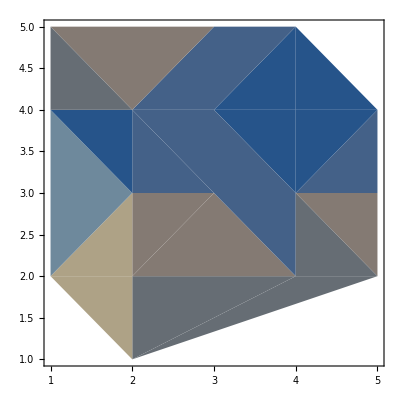

```mathematica
ListDensityPlot[overlapCounts]
```

```mathematica
(*Data instantiate*)
data=RandomVariate[NormalDistribution[],{100,2}];
(*3D histogram whose vertical axis counts the probability (coincidence)*)
Histogram3D[data,10,"PDF",ColorFunction->"Rainbow",AxesLabel->{"X","Y","Frequency"},PlotLabel->"3D Histogram Example"]
(*Smooth discrete data to continuous data with SmoothKernelDistribution function*)
dist=SmoothKernelDistribution[data];
(*Use DensityPlot to delineate the continuous data*)
DensityPlot[PDF[dist,{x,y}],{x,Min[data[[All,1]]],Max[data[[All,1]]]},{y,Min[data[[All,2]]],Max[data[[All,2]]]},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->All,AxesLabel->{"X","Y"},PlotLabel->"2D Density Plot"]
(*Plot the discrete data without smoothing data with the BinCounts function*)
binnedData=BinCounts[data,{Min[data[[All,1]]],Max[data[[All,1]]],1},{Min[data[[All,2]]],Max[data[[All,2]]],1}];
(*Use ListDensityPlot to plot the discrete data*)
ListDensityPlot[Flatten[Table[{Min[data[[All,1]]]+i-1/2,Min[data[[All,2]]]+j-1/2,binnedData[[i,j]]},{i,1,Dimensions[binnedData][[1]]},{j,1,Dimensions[binnedData][[2]]}],1],ColorFunction->"Rainbow"]
```

### 2)Neutrino mass data

```mathematica
(*Input*)
cβ=1/(√2);
mH=1000;(*Mass of new charged doublet Higgs in GeV*)
mS=200;(*Mass of new charged singlet Higgs in GeV*)
me=0.511*10^6;(*Electron mass in eV*)
mmu=106*10^6;(*Muon mass in eV*)
mtau=1777*10^6;(*Tau mass in eV*)
```

```mathematica
YS[Yemu_,Yeta_,Ymuta_,θemu_,θeta_,θmuta_]:={{0,Yemu*Exp[I*θemu],Yeta*Exp[I*θeta]},{-Yemu*Exp[I*θemu],0,Ymuta*Exp[I*θmuta]},{-Yeta*Exp[I*θeta],-Ymuta*Exp[I*θmuta],0}};
YH[Mee_,Mmumu_,Mtata_,Memu_,Meta_,Mmuta_,Mmue_,Mtae_,Mtamu_]:={{Mee,Memu,Meta},{Mmue,Mmumu,Mmuta},{Mtae,Mtamu,Mtata}};
k = (2cβ √(1-cβ^2))/(16 Pi^2)Log[mS^2/mH^2];
Ml=DiagonalMatrix[{me,mmu,mtau}];
```

```mathematica
(*Mixing mass matrix*)
Mν[Yemu_,Yeta_,Ymuta_,θemu_,θeta_,θmuta_,Mee_,Mmumu_,Mtata_,Memu_,Meta_,Mmuta_,Mmue_,Mtae_,Mtamu_]:=k*(Dot[YS[Yemu,Yeta,Ymuta,θemu,θeta,θmuta],Ml,Transpose[YH[Mee,Mmumu,Mtata,Memu,Meta,Mmuta,Mmue,Mtae,Mtamu]]]+Dot[YH[Mee,Mmumu,Mtata,Memu,Meta,Mmuta,Mmue,Mtae,Mtamu],Ml,Transpose[YS[Yemu,Yeta,Ymuta,θemu,θeta,θmuta]]]);
```

```mathematica
(*Diagonalizing mass matrix*)
Eigen[Yemu_,Yeta_,Ymuta_,θemu_,θeta_,θmuta_,Mee_,Mmumu_,Mtata_,Memu_,Meta_,Mmuta_,Mmue_,Mtae_,Mtamu_]:= Eigensystem[Dot[ConjugateTranspose[Mν[Yemu,Yeta,Ymuta,θemu,θeta,θmuta,Mee,Mmumu,Mtata,Memu,Meta,Mmuta,Mmue,Mtae,Mtamu]],Mν[Yemu,Yeta,Ymuta,θemu,θeta,θmuta,Mee,Mmumu,Mtata,Memu,Meta,Mmuta,Mmue,Mtae,Mtamu]]];
(*Eigenvalue*)
EiValue[Eigen_]:=Eigen[[1]];
(*Eigenvectors*)
EiVectors[Eigen_]:=Eigen[[2]];
(*Rearrange the eigenvalue and rotation matrix in NH*)
NHTransposematrix = {{0,0,1},{0,1,0},{1,0,0}};(*the NH rearranging matrix*)
IHTransposematrix = {{0,1,0},{1,0,0},{0,0,1}};(*the IH rearranging matrix*)
(*Subscript[U, PMNS] in NH*)
NHUPMNS[Eigen_]:=Dot[Transpose[EiVectors[Eigen]],NHTransposematrix ];
(*Δm in NH*)
NHDeltaM12[Eigen_]:=EiValue[Eigen][[2]]-EiValue[Eigen][[3]];
NHDeltaM[Eigen_]:=EiValue[Eigen][[1]]-1/2(EiValue[Eigen][[3]]+EiValue[Eigen][[2]]);
(*Subscript[U, PMNS] in IH*)
IHUPMNS[Eigen_]:=Dot[Transpose[EiVectors[Eigen]],IHTransposematrix ];
(*Δm in IH*)
IHDeltaM12[Eigen_]:=EiValue[Eigen][[1]]-EiValue[Eigen][[2]];
IHDeltaM[Eigen_]:=EiValue[Eigen][[3]]-1/2(EiValue[Eigen][[1]]+EiValue[Eigen][[2]])
```

```mathematica
(*Neutrino oscillation function in terms of mixing angle and CP phase*)
c12[U11_,U13_]:=√(Abs[U11]^2/(1-Abs[U13]^2));
s12[U11_,U13_]:=√(1-c12[U11,U13]^2);
c23[U13_,U33_]:=√(Abs[U33]^2/(1-Abs[U13]^2));
s23[U13_,U33_]:=√(1-c23[U33,U13]^2);
s13[U13_]:=Abs[U13];
c13[U13_]:=√(1-s13[U13]^2);
```

```mathematica
cosCP[U11_,U13_,U33_,U21_,U31_]:=(Abs[U21]^2+Abs[U31]^2-(s13[U13]^2+1)*(c12[U11,U13]^2*s23[U13,U33]^2+s12[U11,U13]^2*c23[U13,U33]^2))/(4*c12[U11,U13]*s12[U11,U13]*c23[U13,U33]*s23[U13,U33]*s13[U13]);(*CP phase*)
```

### 3) Parameters scan

#### +) Neutrino data scan

```mathematica
(*Data prepare*)
MagnitudeRange=Range[0,1,0.5];(*Magnitude of YS range*)
Phaserange=Range[0,2*Pi,3];(*Phase of YS range*)
ValueRange=Range[-1,1,0.5];(*YH elements's range*)
(*YSdata=Flatten[Table[{a,b,c,d,e,f},{a,MagnetudeRange},{b,MagnetudeRange},{c,MagnetudeRange},{d,Phaserange},{e,Phaserange},{f,Phaserange}],5];
YHdata=Flatten[Table[{a,b,c,d,e,f,g,h,l},{a,MagnetudeRange},{b,MagnetudeRange},{c,MagnetudeRange},{d,MagnetudeRange},{e,MagnetudeRange},{f,MagnetudeRange},{g,MagnetudeRange},{h,MagnetudeRange},{l,MagnetudeRange}],8];*)
(*YH and YS combined data set*)
YData[Yemu_,Yeta_,Ymuta_,θemu_,θeta_,θmuta_]:=Flatten[Table[{Yemu,Yeta,Ymuta,θemu,θeta,θmuta,Mee,Mmumu,Mtata,Memu,Meta,Mmuta,Mmue,Mtae,Mtamu},{Mee,ValueRange},{Mmumu,ValueRange},{Mtata,ValueRange},{Memu,ValueRange},{Meta,ValueRange},{Mmuta,ValueRange},{Mmue,ValueRange},{Mtae,ValueRange},{Mtamu,ValueRange}],8];
```

```mathematica
ABC=Flatten[Table[YData[Yemu,1,1,1,1,1],{Yemu,MagnetudeRange}],1];(*Limitation is roughly 10^8 x15 numbers*)
```

```mathematica
(*Data prepare*)
MagnitudeRange=Range[0.01,1,0.2];(*Magnitude of YS range*)
Phaserange={0,Pi/4,Pi/2};(*Phase of YS range*)
ValueRange={-0.1,0.1};(*YH elements's range*)
YData=ArrayReshape[Table[{Yemu,Yeta,Ymuta,θemu,θeta,θmuta,Mee,Mmumu,Mtata,Memu,Meta,Mmuta,Mmue,Mtae,Mtamu},{Yemu,MagnitudeRange},{Yeta,MagnitudeRange},{Ymuta,MagnitudeRange},{θemu,Phaserange},{θeta,Phaserange},{θmuta,Phaserange},{Mee,ValueRange},{Mmumu,ValueRange},{Mtata,ValueRange},{Memu,ValueRange},{Meta,ValueRange},{Mmuta,ValueRange},{Mmue,ValueRange},{Mtae,ValueRange},{Mtamu,ValueRange}],{Length[MagnitudeRange],Length[MagnitudeRange],Length[MagnitudeRange]*Length[Phaserange]^3*Length[ValueRange]^9,15}];
```

```mathematica
(*Parameter scan*)
DataY=Flatten[Table[{MagnitudeRange[[Yemu]],MagnitudeRange[[Yeta]],Length[Select[Eigen@@#&/@YData[[Yemu,Yeta]],(0.25<s12[NHUPMNS[#][[1,1]],NHUPMNS[#][[1,3]]]^2<0.354)&&(0.0185<s13[NHUPMNS[#][[1,3]]]^2<0.0246)&&(0.379<s23[NHUPMNS[#][[1,3]],NHUPMNS[#][[3,3]]]^2<0.616)&&(6.93*10^-5<NHDeltaM12[#]<7.97*10^-5)&&(2.37*10^-3<NHDeltaM[#]<2.63*10^-3)&&(Cos[0.92*Pi]<cosCP[NHUPMNS[#][[1,1]],NHUPMNS[#][[1,3]],NHUPMNS[#][[3,3]],NHUPMNS[#][[2,1]],NHUPMNS[#][[3,1]]]<Cos[1.99*Pi])&]]},{Yemu,1,5,1},{Yeta,1,5,1}],1];
```

```mathematica
DataY
```

{{0.01,0.01,0},{0.01,0.21,0},{0.01,0.41,0},{0.01,0.61,0},{0.01,0.81,0},{0.21,0.01,0},{0.21,0.21,0},{0.21,0.41,0},{0.21,0.61,0},{0.21,0.81,0},{0.41,0.01,0},{0.41,0.21,0},{0.41,0.41,0},{0.41,0.61,0},{0.41,0.81,0},{0.61,0.01,0},{0.61,0.21,0},{0.61,0.41,0},{0.61,0.61,0},{0.61,0.81,0},{0.81,0.01,0},{0.81,0.21,0},{0.81,0.41,0},{0.81,0.61,0},{0.81,0.81,0}}

```mathematica
c=0.0001;
Ftarget[Yemu_,Yeta_,Ymuta_,θemu_,θeta_,θmuta_]:=Module[{M=Eigen[Yemu,Yeta,Ymuta,θemu,θeta,θmuta,c,c,c,c,c,c,c,c,c]},UPMNS=NHUPMNS[M];(NHDeltaM12[M]-7.37*10^(-5))^2+(NHDeltaM[M]-2.5*10^(-3))^2+(s12[UPMNS[[1,1]],UPMNS[[1,3]]]-0.297)^2+(s13[UPMNS[[1,3]]]-0.0214)^2+(s23[UPMNS[[1,3]],UPMNS[[3,3]]]-0.437)^2+(cosCP[UPMNS[[1,1]],UPMNS[[1,3]],UPMNS[[3,3]],UPMNS[[2,1]],UPMNS[[3,1]]]-Cos[1.35*Pi])^2];
result=NMinimize[{Ftarget[Yemu,Yeta,Ymuta,θemu,θeta,θmuta],1>{Yemu,Yeta,Ymuta}>0,2Pi>{θemu,θeta,θmuta}≥0},{Yemu,Yeta,Ymuta,θemu,θeta,θmuta}];
```

Eigensystem::eivec0: Unable to find all eigenvectors.

NMinimize::nrnum: The function value 1.98676×10^8-0.750802 ⅈ is not a real number at {Yemu,Yeta,Ymuta,θemu,θeta,θmuta} = {0.974797,0.620288,0.629657,6.21398,1.92627,3.89653}.

General::stop: Further output of NMinimize::nrnum will be suppressed during this calculation.

```mathematica
matrix[x_,y_]:={{x,x+y,y},{x^2,y,x},{x,y-x,y}};
Eig[x_,y_]:= Eigensystem[Dot[ConjugateTranspose[matrix[x,y]],matrix[x,y]]];
```

```mathematica
Ftarget[x_,y_]:=Module[{UPMNS=NHUPMNS[Eig[x,y]]},UPMNS[[1,1]]-0.8];
result=NMinimize[{Ftarget[x,y]},{x,y}];
```

#### +) LFV decay scan

```mathematica
MagnitudeRange=Range[0.01,1,0.2];(*Magnitude of YS range*)
Phaserange={0,Pi/4,Pi/2};(*Phase of YS range*)
ValueRange={-0.1,0.1};(*YH elements's range*)
YData=ArrayReshape[Table[{Yemu,Yeta,Ymuta,θemu,θeta,θmuta,Mee,Mmumu,Mtata,Memu,Meta,Mmuta,Mmue,Mtae,Mtamu},{Yemu,MagnitudeRange},{Yeta,MagnitudeRange},{Ymuta,MagnitudeRange},{θemu,Phaserange},{θeta,Phaserange},{θmuta,Phaserange},{Mee,ValueRange},{Mmumu,ValueRange},{Mtata,ValueRange},{Memu,ValueRange},{Meta,ValueRange},{Mmuta,ValueRange},{Mmue,ValueRange},{Mtae,ValueRange},{Mtamu,ValueRange}],{Length[MagnitudeRange],Length[MagnitudeRange],Length[MagnitudeRange]*Length[Phaserange]^3*Length[ValueRange]^9,15}];
```

```mathematica
a=0.00015;
b=Pi/4;
c=0.0000009;
FakeData={0.0009,0.0001,0.00015,b,b,b,0.00000085,0.00000089,0.0000007,0.0000002,0.0000007,0.0000005,0.0000007,0.0000008,0.0000002};
valueEigen=Eigen@@FakeData;
s12[NHUPMNS[valueEigen][[1,1]],NHUPMNS[valueEigen][[1,3]]]^2
s13[NHUPMNS[valueEigen][[1,3]]]^2
s23[NHUPMNS[valueEigen][[1,3]],NHUPMNS[valueEigen][[3,3]]]^2
NHDeltaM12[valueEigen]
NHDeltaM[valueEigen]
```

0.334263

0.0243989

0.410613

0.00020554

0.00010277